```mathematica
xx=N[Table[2^i,{i,-4,7}]];
Print["X=",Length[xx],xx];
nrange=6;
exp=2.5;
ee=N[Table[exp^j,{j,-nrange,nrange}]];
Print["Lambda=",Length[ee],ee];
Print["Npoint,Nexp=",{Length[xx],Length[ee]}]
(* 
Start Fitting: M*x=c
*)
(* dimM=nexp*npoint *)
mat=Table[Table[N[BesselK[0,ee[[j]]*xx[[i]]]],
{j,1,Length[ee]}],{i,1,Length[xx]}];
(* dimB=npoint *)
bvec=Table[N[1/xx[[i]]],{i,1,Length[xx]}];
coeff=PseudoInverse[mat].bvec;
(* Errors: errors=Abs[1/x-funX]/.x->xx *)
errors=Abs[mat.coeff-bvec]
Max[errors]
```

X=12{0.0625,0.125,0.25,0.5,1.,2.,4.,8.,16.,32.,64.,128.}

Lambda=13{0.004096,0.01024,0.0256,0.064,0.16,0.4,1.,2.5,6.25,15.625,39.0625,97.6563,244.141}

Npoint,Nexp={12,13}

{2.4869×10^-14,1.06581×10^-14,2.04281×10^-14,1.33227×10^-14,1.46549×10^-14,1.12133×10^-14,5.10703×10^-15,4.996×10^-15,1.9984×10^-15,5.55112×10^-16,1.01655×10^-15,1.21431×10^-17}

2.4869×10^-14

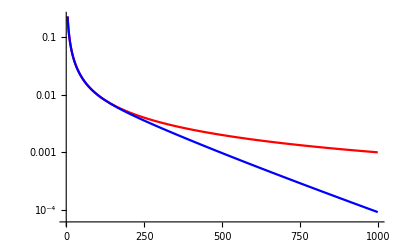

```mathematica
Clear[x];
funX=Table[BesselK[0,x*ee[[j]]],{j,1,Length[ee]}].coeff;
funX;
LogPlot[
{1/x,funX},{x,10^(-10),1000},PlotStyle->{Red,Blue},PlotRange->{0,1000}
]
```

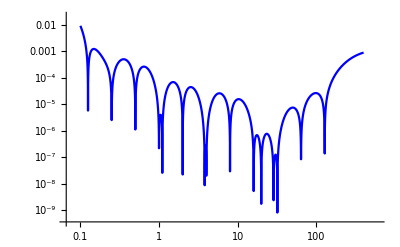

```mathematica
Show[
LogLogPlot[Abs[1/x-funX],{x,0.1,400},PlotStyle->{Blue},PlotRange->Full],
ListPlot[Log[errors],PlotMarkers->Automatic,PlotStyle->{Red}]
]
```

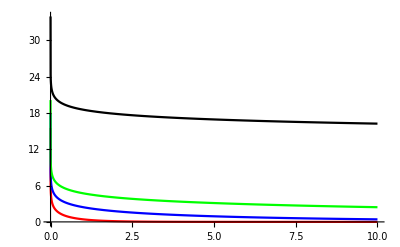

```mathematica
Plot[{BesselK[0,x],BesselK[0,0.1x],BesselK[0,0.01x],BesselK[0,0.00000001x]},{x,0,10},PlotRange->Full,PlotStyle->{Red,Blue,Green,Black}]
```

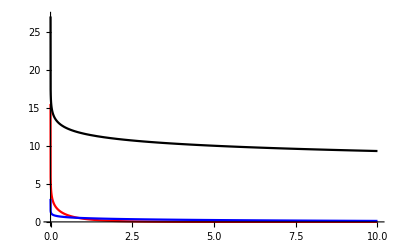

```mathematica
Plot[{BesselK[0,x],0.163578032BesselK[0,5.7449*10^(-9)x]-2.61827453,
BesselK[0,10^{-5}x]},{x,0,10},PlotRange->Full,PlotStyle->{Red,Blue,Black}]
```

```mathematica
Table[N[BesselK[0,10^{-18}i]],{i,0,10}]
```

{{∞},{41.5625},{40.8693},{40.4639},{40.1762},{39.953},{39.7707},{39.6166},{39.483},{39.3652},{39.2599}}

```mathematica
N[1/Sqrt[2Pi]]/2
```

0.199471